```mathematica
(* First we want to find the Basic Reproduction Number so that we can determine criterion to solve the numerical equations. We use the "next generation method" *)
```

```mathematica
V={{d+α, k}, {-α, d+k}}
```

{{d+α,k},{-α,d+k}}

```mathematica
Vinv = Inverse[V]
```

{{(d+k)/(d^2+d k+d α+2 k α),-k/(d^2+d k+d α+2 k α)},{α/(d^2+d k+d α+2 k α),(d+α)/(d^2+d k+d α+2 k α)}}

```mathematica
F = {{β*S0, 0},{0,0}}
```

{{S0 β,0},{0,0}}

```mathematica
F.Vinv
```

{{((d+k) S0 β)/(d^2+d k+d α+2 k α),-(k S0 β)/(d^2+d k+d α+2 k α)},{0,0}}

```mathematica
(* Since this is an upper triangular matrix, the eigenvalues are on the diagonal. The spectral radius is therefore: ((d+k) S0 β)/(d^2+d k+d α+2 k α) *)
```

```mathematica
(* We now want to find the numerical solutions. *)
```

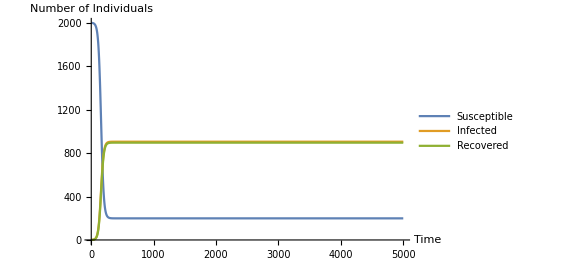

0.099995

```mathematica
equations = {
s'[t] == A - β*s[t]*i[t]-d*s[t],
i'[t] == β*s[t]*i[t]-(d+α)*i[t]+k*r[t],
r'[t] == α*i[t] -(d+k)*r[t],
s[0]==A/d, i[0]==1,r[0]==0
};
(* R0<1 is when beta 0.00056, 
R0>1 is when beta 0.00057 *)
params = {A->10,d->0.005,β->0.00005,k->1/2.0 ,α->1/2.0 };
totaltime = 5000;
solutions = NDSolve[equations/.params,{s[t], i[t], r[t]},{t,0,totaltime}];
Plot[{Evaluate[s[t]/.solutions],Evaluate[i[t]/. solutions],Evaluate[r[t]/.solutions]}, {t,0,totaltime},PlotLegends->Placed[{"Susceptible", "Infected", "Recovered"},{0.85,0.75}],AxesLabel->{"Time","Number of Individuals"},Axes->True]
R0 =((d+k) *(A/d)* β)/(d^2+d k+d α+2 k α)/.params
```